# Test Data Trace Plotting

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

(last updated:  Mon 17 Feb 2014 11:22:55)

<<Set JLink` java stack size to 3072Mb>>

«JavaObject[nounou.DataReader]»

```mathematica
ShowJavaConsole[]
```

«JavaObject[com.wolfram.jlink.ui.ConsoleWindow]»

## Load Data

```mathematica
testDataFileDirectory = "V:\\docs\\k.VSDdata\\project.SPP\\Nlx\\SPP010\\2013-12-02_17-07-31";
```

```mathematica
(* FileNames[testDataFileDirectory<>"\\*"] *)
```

```mathematica
testFiles4=FileNames[testDataFileDirectory<>"\\Tet4*.ncs"]
```

{V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4a.ncs,V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4b.ncs,V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4c.ncs,V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4d.ncs}

```mathematica
(*Methods[NN]*)
```

```mathematica
$NNReader = NN`newReader[]
```

«JavaObject[nounou.DataReader]»

```mathematica
$NNReader@load[testFiles4]
```

## Accessor Tests

```mathematica
$NNReader@dataSummary[]
```

DataReader loaded data summary:
     header : XHeaderNull
     data   : XData(4 channels, 1 segments, with lengths Vector(151597056), fs=32000.0)
      (filt): XDataFilterFIR: kernel null (off)
     dataAux: XDataNull
     layout : XLayoutNull
     mask   : XMaskNull
     events : XEventsNull
     spikes : XSpikesNull

```mathematica
$NNReader@dataGetDecimate[]
```

16

```mathematica
{$NNReader@dataAbsUnit[], $NNReader@dataAbsGain[], $NNReader@dataAbsOffset[]}
```

{microV,0.0000298032,0.}

```mathematica
{$NNReader@dataChannelNames[], $NNReader@dataChannelName[0], $NNReader@dataChannelCount[]}
```

{{Tet4a,Tet4b,Tet4c,Tet4d},Tet4a,4}

```mathematica
$NNReader@dataSampleRate[]
```

2000.

## Raw Access Tests

```mathematica
$NNReader@dataSetFilterOff[]
```

```mathematica
Length[$NNReader@dataTrace[0, NN`frameRange[0,5000,10], 0]]
```

501

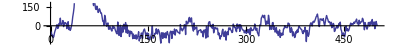

```mathematica
grOri=ListLinePlot[$NNReader@dataTraceAbs[0, NN`frameRange[0,5000,10], 0],AspectRatio->1/10]
```

```mathematica
$NNReader@dataSampleRate[]
```

2000.

```mathematica
$NNReader@dataSetFilterHz[0.5,20]
```

```mathematica
$NNReader@dataFIR[]@toString[]
```

XDataFilterFIR: kernel class breeze.signal.support.FIRKernel1D multiplier: 256: FIRKernel1D(firwin): 1024 taps, DenseVector(5.0E-4, 0.02), Hamming window (0.54, 0.46), zeroPass=false, nyquist=1.0, scale=true, multiplier: 256

```mathematica
Length[$NNReader@dataTrace[0, NN`frameRange[0,5000,10], 0]]
```

501

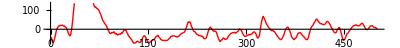

```mathematica
grFilt=ListLinePlot[$NNReader@dataTraceAbs[0, NN`frameRange[0, 5000,10], 0],AspectRatio->1/10,PlotStyle->Red]
```

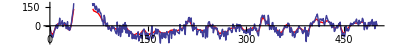

```mathematica
Show[grFilt,grOri,PlotRange->All]
```

```mathematica
$NNReader@dataSetFilterHz[0,1000]
```

```mathematica
$NNReader@dataFIR[]@kernel[] == Null
```

True

## NNTracePlot

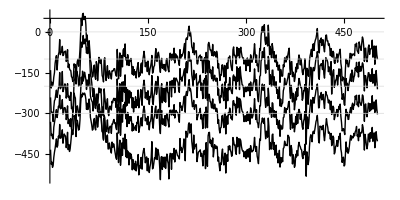

```mathematica
NNTracePlot[ Range[0,3], 0 ;; 5000 ;; 10 ]
```